Valores de parametros usados como ejemplo.

```mathematica
β = 0.707; Ω = 0.25; h = 1;
```

```mathematica
alphaMas= NDSolve[{y'[t]- I Ω  y[t]^2 + 2 I  (β^2)t y[t] + I  Ω==0,y[0]==0}, y, {t,-40,40}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Plot[Im[Evaluate[y[t]  /. alphaMas]], {t, -40, 40}]
```

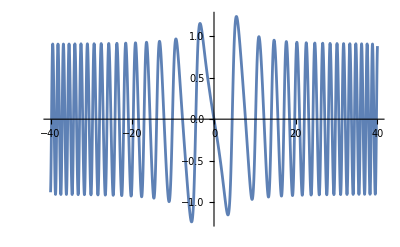

## Resolución del sistema por pasos

Ecuación diferencial para α_+

```mathematica
alphaMas= NDSolveValue[{y'[t]- I Ω  y[t]^2 + 2 I  (β^2)t y[t] + I  Ω==0,y[0]==0}, y, {t,-40,40}]
```

InterpolatingFunction[…]

```mathematica
Plot[Im[alphaMas[t]], {t, -40, 40}]
```

-Graphics-

```mathematica
alphaMas[12]
```

0.57469+0.25698 ⅈ

Ecuación diferencial para α_z

```mathematica
alphaZ[T_] := I(Ω NIntegrate[alphaMas[t], {t, 0 , T}] - (β^ 2)( T^2)( 0.5))
```

```mathematica
alphaZ[30]
```

0.335219-30.2466 ⅈ

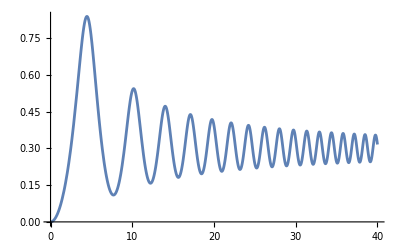

```mathematica
Plot[Re[alphaZ[t]], {t, 0, 40}]
```

A partir de la expresión para α_z creamos una tabla de valores y los interpolamos para obtener una “función numerica integrable” de α_z

```mathematica
alphaZInter = Interpolation[Table[alphaZ[t],{t,0,30}]]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[alphaZInter[t], {t, 1, 10}]
```

3.02247-13.2524 ⅈ

Ecuación diferencial para α_-

```mathematica
alphaMenos[T_] := -I Ω NIntegrate[Exp[2 alphaZInter[t]], {t, 1, T}]
```

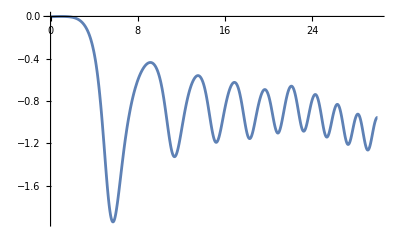

```mathematica
Plot[Re[alphaMenos[t]], {t, 0, 30}]
```

## Resolución del sistema completo

```mathematica
Clear[alphaMas, alphaMenos, alphaZ, Ω, β]
```

Primer ejemplo de valores para los parámetros

```mathematica
β = 0.707; Ω = 0.25;
```

Segundo ejemplo de valores

```mathematica
β = 0.3; Ω = 0.2;
```

Tercer ejemplo de valores

```mathematica
β = 0.3; Ω = 0.5;
```

En la siguiente celda ejecutamos el comando NDSolveValue para resolver el sistema completo de ecuaciones diferenciales de forma númerica. En esta expresión las funciones x(t), y(t), z(t) representan las funciones α_+(t), α_z(t) y α_-(t) respectivamente.

```mathematica
{alphaMas,alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + I Ω(1 + x[t]^2)== 0 ,y'[t] == I(Ω x[t] - (β^2 )t),z'[t]Exp[-2 y[t]]+ I Ω == 0, x[-60]==y[-60]==z[-60]== 0},{x,y, z},{t,-100, 100}]
```

{InterpolatingFunction[{{-100., 100.}}, <>],InterpolatingFunction[{{-100., 100.}}, <>],InterpolatingFunction[{{-100., 100.}}, <>]}

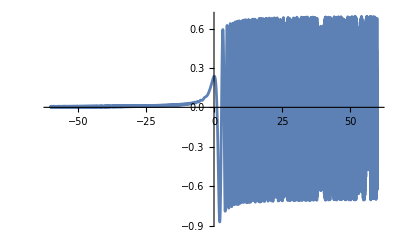

```mathematica
Plot[Re[alphaMas[t]], {t, -60, 60}]
```

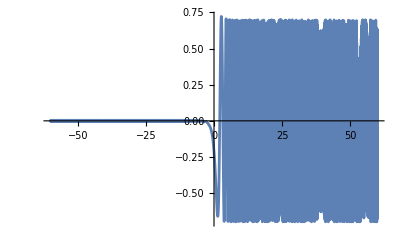

```mathematica
Plot[Im[alphaMas[t]], {t, -60, 60}]
```

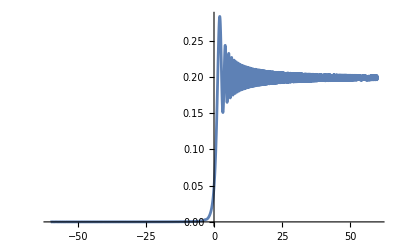

```mathematica
Plot[Re[alphaZ[t]], {t, -60, 60}]
```

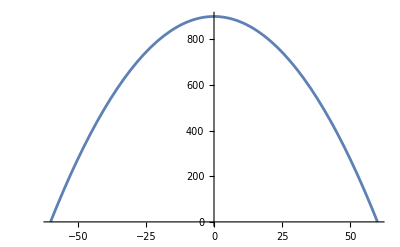

```mathematica
Plot[Im[alphaZ[t]], {t, -60, 60}]
```

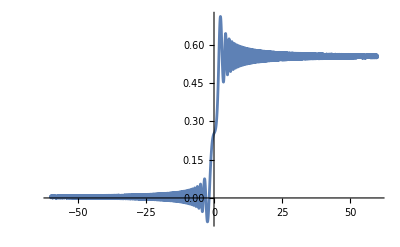

```mathematica
Plot[Re[alphaMenos[t]], {t, -60, 60}]
```

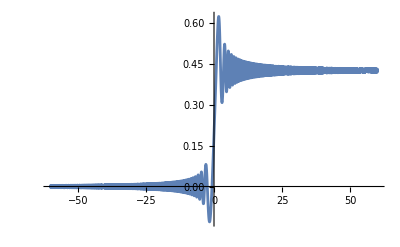

```mathematica
Plot[Im[alphaMenos[t]], {t, -60, 60}]
```

### Probabilidades de Transición

Valor limite/estacionario esperado (t →  ∞)

```mathematica
Exp[-π(Ω^2/β^2)]
```

0.675152

Probabilidad de ir del estado base al estado excitado considerando que el estado inicial es el estado base (P_g->e(t))

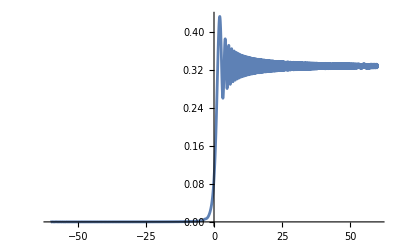

```mathematica
Plot[(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], {t, -60, 60}]
```

Probabilidad de transición al estado base considerando que el estado inicial es el estado base (P_g->g(t))

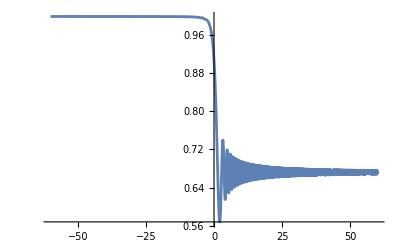

```mathematica
Plot[Abs[Exp[- alphaZ[t]] ]^2, {t, -60, 60}]
```

Las tres funciones en un mismo grafico

```mathematica
Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2,Exp[-π(Ω^2/β^2)]}, {t, -60, 60}, 
PlotLabel->Style["Probabilidades de transición  β = 0.707 , Ω = 0.25, ψ (0) = |g⟩ ", 16, FontFamily->"Times New Roman", Black],
PlotLegends-> {"P_(g -> e)(t)", "P_(g -> g)(t)", "exp(-π Ω^2 / β^2)"},PlotLabels->{"","",Style["0.675", 14,FontFamily->"Times New Roman",GrayLevel[0.26]]},
AxesLabel-> {Style["t",16,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_g(t)",16,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500]
```

-Graphics-

Probabilidad de ir del estado excitado al estado base considerando que el estado inicial es el estado excitado (P_e->g(t))

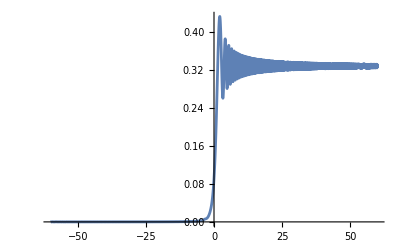

```mathematica
Plot[(Abs[alphaMenos[t]]^2) Exp[-2Re[alphaZ[t]]], {t, -60, 60}]
```

Probabilidad de transición al estado excitado considerando que el estado inicial es el estado excitado (P_e->e(t))

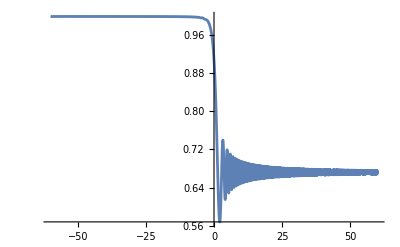

```mathematica
Plot[Abs[Exp[alphaZ[t]] + Exp[-alphaZ[t]] alphaMas[t] alphaMenos[t]]^2, {t, -60, 60}]
```

Ambas funciones en un gráfico

```mathematica
Plot[{(Abs[alphaMenos[t]]^2) Exp[-2Re[alphaZ[t]]], Abs[Exp[alphaZ[t]] + Exp[-alphaZ[t]] alphaMas[t] alphaMenos[t]]^2, Exp[-π(Ω^2/β^2)]}, {t, -60, 60},
 PlotLabel->Style["Probabilidades de transición β = 0.707, Ω = 0.25, ψ (0) = |e⟩ ", 16, FontFamily->"Times New Roman", Black],
PlotLegends-> {"P_(e -> g)(t)", "P_(e -> e)(t)", "exp(-π Ω^2 / β^2)"}, PlotLabels->{"","",Style["0.675", 14,FontFamily->"Times New Roman",GrayLevel[0.26]]},AxesLabel-> {Style["t",16,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_e(t)",16,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500]
```

-Graphics-

## Integrales del espectro fisico

Caso 1: Consideramos que el estado inicial es el estado base.

```mathematica
I1[Γ_, ω_, T_]:= NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2, {t, 0, T}]
```

```mathematica
I2[Γ_, ω_, T_]:= NIntegrate[-Exp[(Γ+I ω)t]Exp[-2alphaZ[t]]alphaMas[t]^2, {t,0,T}]
```

```mathematica
I3[Γ_, ω_, T_]:= NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZ[t]]alphaMenos[t],{t,0,T}]
```

```mathematica
I4[Γ_,ω_,T_]:= NIntegrate[Exp[(Γ+I ω)t](alphaMas[t]+Exp[-2alphaZ[t]](alphaMas[t]^2)alphaMenos[t]), {t,0,T}]
```

```mathematica
S1[Γ_,ω_,T_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T]I2[Γ, ω,T]+I3[Γ, ω,T]I4[Γ, ω,T])
```

```mathematica
S1[0.1,10,25]
```

0.00688718-3.28075×10^-8 ⅈ

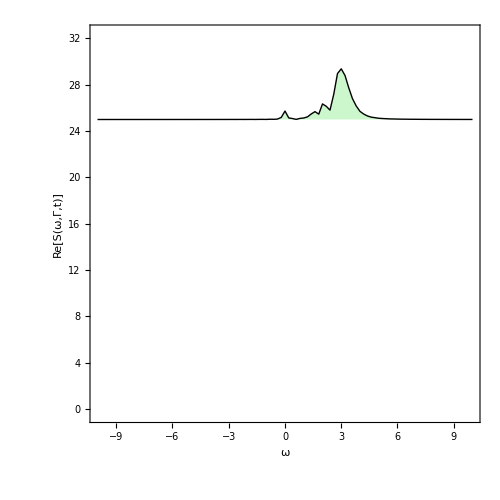

```mathematica
G1=ListLinePlot[ParallelTable[{ω,25+Re[S1[0.1,ω,20]]},{ω,-10,10,0.2}],PlotRange->{-0.5,32.5},Filling->25,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=40",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["Re[S(ω,Γ,t)]",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.3,t=40",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

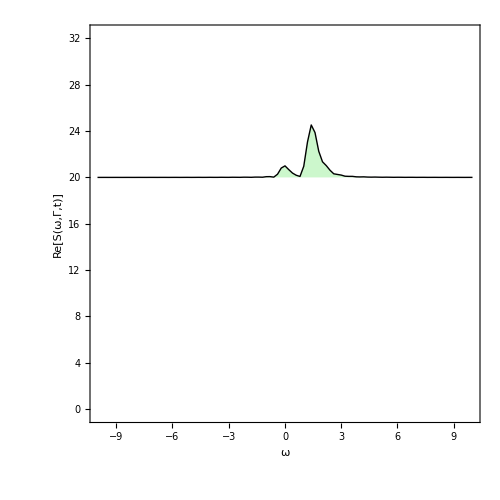

```mathematica
G2 = ListLinePlot[ParallelTable[{ω,20 + Re[S1[0.1,ω,10]]},{ω,-10,10,0.2}],PlotRange->{-0.5,32.5},Filling->20,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=10",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["Re[S(ω,Γ,t)]",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.25,t=10",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

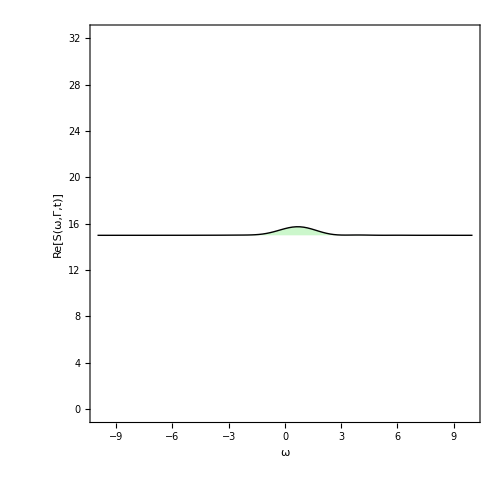

```mathematica
G3 = ListLinePlot[ParallelTable[{ω,15+Re[S1[0.1,ω,3]]},{ω,-10,10,0.2}],PlotRange->{-0.5,32.5},Filling->15,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=3",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["Re[S(ω,Γ,t)]",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.25,t=5",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

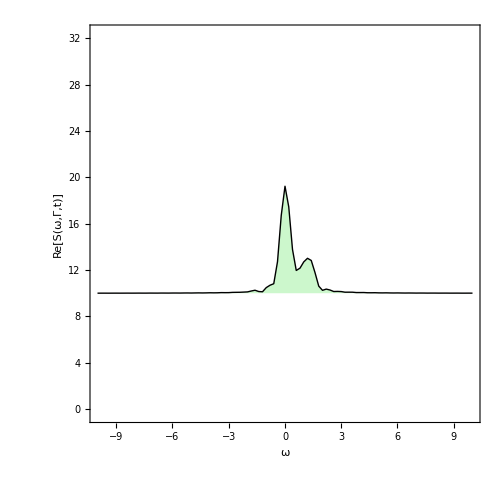

```mathematica
G4 = ListLinePlot[ParallelTable[{ω,10 + Re[S1[0.1,ω,-10]]},{ω,-10,10,0.2}],PlotRange->{-0.5,32.5},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-10",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["Re[S(ω,Γ,t)]",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.25,t=-10",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

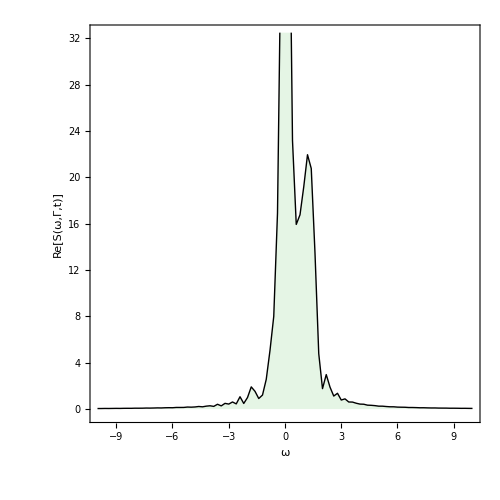

```mathematica
G5 = ListLinePlot[ParallelTable[{ω,Re[S1[0.1,ω,-20]]},{ω,-10,10,0.2}],PlotRange->{-0.5,32.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-20",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["Re[S(ω,Γ,t)]",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.25,t=-20",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.65,0],Opacity[.1]]]
```

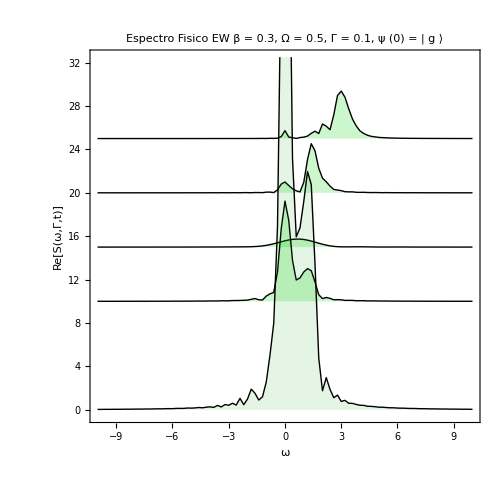

```mathematica
Show[G1,G2,G3,G4,G5, PlotLabel->Style["Espectro Fisico EW \n β = 0.3, Ω = 0.5, Γ = 0.1, ψ (0) = | g ⟩ ", 18, FontFamily->"Times New Roman", Black]]
```

Caso 2: Consideramos que el estado inicial es el estado excitado

```mathematica
L1[Γ_,ω_,T_]:= NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t], {t,0,T}]
```

```mathematica
L2[Γ_,ω_,T_]:= NIntegrate[Exp[(Γ+I ω)t](-alphaMas[t] - Exp[-2alphaZ[t]]alphaMas[t]alphaMenos[t]), {t,0,T}]
```

```mathematica
L3[Γ_,ω_,T_]:= NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]], {t,0,T}]
```

```mathematica
L4[Γ_,ω_,T_]:= NIntegrate[Exp[(Γ+I ω)t](Exp[alphaZ[t]] + Exp[-alphaZ[t]]alphaMas[t]alphaMenos[t])^2, {t,0,T}]
```

```mathematica
S2[Γ_,ω_,T_]:=2Γ Exp[-2Γ T](L1[Γ,ω,T]L2[Γ,ω,T]+L3[Γ,ω,T]L4[Γ,ω,T])
```